# Report Project 1

Course code: IX1500
Date: 2019-09-12

Magnus Fredriksson, magfred@kth.se
Fredrik Öberg, fobe@kth.se

Task a: Probability by census

## Summary

### Task

Assume that you play a variant of a poker game with five cards that is using a subset of one ordinary deck of cards. The subset considered is cards valued 7, 8, 9,10,J,Q,K,A from the one decks, in total 32 cards. Allow A-7-8-9-10 as a low straight or straight flush.

Calculate the exact probability of the following hands using the census method.

one pair

two pairs

three of a kind

straight

full house

flush

four of a kind

straight flush

nothing

Compare and discuss the probabilities of the above variant poker game to the probabilities for a normal poker game with a standard 52 card deck.

### Result

We started the assignment with calculating the total number of starting hands. We applied filters to the total subset for the wanted cases. With the number of hands that matched each case we divided those numbers with the total and got the probability of getting each specific starting hand. We got the results as follows:

Exact probability of Pair
480/899 or approx. 0.534

Exact probability of two pairs
108/899 or approx. 0.12

Exact probability of Three of a Kind
48/899 or approx. 0.053

Exact probability of Straight
1275/50344 or approx. 0.0253

Exact probability of Full House
6/899 or approx. 0.00667

Exact probability of Flush
51/50344 or approx. 0.001

Exact probability of Four of a Kind
1/899 or approx. 0.0011

Exact probability of Straight Flush
5/50344 or approx. 0.0001

Exact probability of nothing
13005/50344 or approx . 0.258

We then did the same for the full deck of 52 cards to compare the probabilities.
The computations for this part were much more intensive, since the subset of five card hands was about 10 times as large as for the 32 card deck.This is the result of the 32 card deck.

"Hand" | "Prob. 32" | "Prob. 52"
"Pair" | 0.533927 | 0.422569
"Two Pair" | 0.120133 | 0.047539
"Three of a Kind" | 0.0533927 | 0.0211285
"Straight" | 0.0253258 | 0.00392465
"Full House" | 0.00667408 | 0.00144058
"Flush" | 0.00101303 | 0.0019654
"Four of a Kind" | 0.00111235 | 0.000240096
"Straight Flush" | 0.0000993167 | 0.0000153908
"Nothing" | 0.258323 | 0.501177

As can be seen from the table above, there was an almost universal decrease in probability for any given hand, with the exception of Flush and no hand.
The flush exception can be explained by the fact that since the probability of drawing a card in a given color is the same as that colors proportion of the remaining cards. 
After one club card has already been drawn, the chance of drawing another in the 52 card deck, is much closer to 4 than in the 32 card deck, since in the 32 card deck 1/8 of the clubs have been exhausted, compared to only 1/13 in the 52 card deck.
The same can be argued for the no hand option.

## Code

```mathematica
ClearAll["`*"]
```

Creates a matrix representing a deck of cards with values from 7 to A.

```mathematica
deckOfCards=Join[Table[{1, i},{i,7,14}],Table[{2, i},{i,7,14}],Table[{3, i},{i,7,14}],Table[{4, i},{i,7,14}]];
Count[deckOfCards, _]
fullDeckOfCards = Join[Table[{1, i}, {i,2,14}], Table[{2, i}, {i,2,14}], Table[{3, i}, {i,2,14}], Table[{4, i}, {i,2,14}]];
```

32

Creates a matrix representing every single combinations of a five card hand.

```mathematica
hands = Subsets[deckOfCards, {5}];
fullDeckHands = Subsets[fullDeckOfCards, {5}];
```

Setup filters for each specific hand variation based on value and/or color.

```mathematica
pairQ[{___, x_,x_,___, y_,y_ ,___}/;x≠y]:=False; (* Filters out all two pair hands *)
pairQ[{___,x_,x_,x_, ___}]:=False; (*  Filters out all three of a kind hands *)
pairQ[{___,x_,x_,___}]:=True; (* Matches pairs*)
pairQ[{___}]:=False;
```

```mathematica
twoPairQ[{___,x_,x_,x_, ___}]:=False; (*  Filters out all thre of a kin, full house and four of a kind hands*)
twoPairQ[{___, x_,x_,___, y_,y_ ,___}/;x≠y]:=True; (* Matches two pairs *)
twoPairQ[{___}]:=False ;
```

```mathematica
threeofAKindQ[{x_, x_,x_, y_,y_}]:=False; (* Filters full house with a high pair*)
threeofAKindQ[{x_, x_, y_,y_, y_}]:=False; (* Filters house with a low pair *)
threeofAKindQ[{___, x_,x_,x_,x_,___}]:=False; (* Filters four of a kind *)
threeofAKindQ[{___,x_,x_,x_, ___}]:=True; (* Matching three of a kind *)
threeofAKindQ[{___}]:=False;
```

```mathematica
straightQ[{v_, x_,y_,z_,w_}/; x == v+1 && y==x+1 && z == y+1 && w == z+1 ]:=True; (* Matches general straights *)
straightQ[{v_, x_,y_,z_,w_}/;  x == v+1 && y==x+1 && z == y+1 && w == z+4  ]:=True; (* Matching low straights, starting with an ace *)
straightQ[{___}]:=False ;

straightQFullDeckQ[{v_, x_,y_,z_,w_}/; x == v+1 && y==x+1 && z == y+1 && w == z+1 ]:=True; (* Matches general straights *)
straightQFullDeckQ[{v_, x_,y_,z_,w_}/;  x == v+1 && y==x+1 && z == y+1 && w == z+9  ]:=True; (* Matching low straights, starting with an ace *)
straightQFullDeckQ[{___}]:=False ;
```

```mathematica
FoakQ[{___, x_, x_,x_, x_,___}]:=True; (* Matches Three of a kind *)
FoakQ[{___}]:=False ;
```

```mathematica
flushQ[{x_,x_,x_,x_,x_}] := True; (* Matches flush hands*)
flushQ[{___}] := False;
```

```mathematica
fullHouseQ[{x_, x_,x_, y_,y_}]:=True; (* Matches full house with a low/high pair *)
fullHouseQ[{x_, x_, y_,y_,y_}]:=True;
fullHouseQ[{___}]:=False;
```

```mathematica
filterOnlyBothQ[{x_, x_} /; x== True] := True;
filterOnlyBothQ[{___}] := False;
```

```mathematica
filterOnlyFirstQ[{x_, y_} /;x == True && x ≠  y] := True;
filterOnlyFirstQ[{___}] := False;
```

```mathematica
filterOnlySecondQ[{x_, y_} /;x == False && x ≠  y] := True;
filterOnlySecondQ[{___}] := False;
```

```mathematica
filterOnlyNeitherQ[{x_, x_} /;x == True] := True;
filterOnlyNeitherQ[{___}] := False;
```

```mathematica
extractValue[x_] := Sort[x[[1;;5,2;;2]]];
extractColor[x_] := Sort[x[[1;;5, 1;;1]]];
```

```mathematica
pairs = Map[pairQ, Map[extractValue,hands ]];
pairCount = Count[pairs, True]
pairProb =pairCount / Length[hands]
```

107520

480/899

```mathematica
twoPairs = Map[twoPairQ, Map[extractValue,hands]];
twoPairsCount = Count[twoPairs, True]
twoPairsProb =twoPairsCount / Length[hands]
```

24192

108/899

```mathematica
threeOfAKind = Map[threeofAKindQ, Map[extractValue,hands]];
threeOfAKindCount = Count[threeOfAKind, True]
threeOfAKindProb = threeOfAKindCount / Length[hands]
```

10752

48/899

```mathematica
straight = Map[straightQ, Map[extractValue,hands]];
straighCount = Count[straight, True]; 
flush = Map[flushQ, Map[extractColor,hands]];
straightCount = Count[Map[filterOnlyFirstQ, Transpose[{straight, flush}]], True]
straightProb = straightCount / Length[hands]
```

5100

1275/50344

```mathematica
fullHouse = Map[fullHouseQ, Map[extractValue, hands]];
fullHouseCount = Count[fullHouse, True]
fullHouseProb = fullHouseCount / Length[hands]
```

1344

6/899

```mathematica
flushCount = Count[Map[filterOnlyFirstQ, Transpose[{flush, straight}]], True]
flushProb =flushCount/Length[hands]
```

204

51/50344

```mathematica
foak= Map[FoakQ, Map[extractValue,hands]];
foakCount = Count[foak, True]
foakProb =foakCount / Length[hands]
```

224

1/899

```mathematica
straightFlush = Map[filterOnlyBothQ, Transpose[{flush, straight}]];
straightFlushCount = Count[straightFlush, True]
straightFlushProb = straightFlushCount / Length[hands]
```

20

5/50344

```mathematica
nothingCount = Count[hands, _] - (pairCount + twoPairsCount + threeOfAKindCount + straightCount  + fullHouseCount + flushCount + foakCount + straightFlushCount) 
nothingProb =nothingCount / Length[hands]
```

52020

13005/50344

```mathematica
(* The probabilities for the 52 deck version *)
(* Pairs *)
fdPairs = Count[Map[pairQ, Map[extractValue,fullDeckHands ]], True];
fdPairsP = N[fdPairs /  Length[fullDeckHands]]
```

0.422569

```mathematica
(* Two Pairs *)
fdTwoPairs = Count[Map[twoPairQ, Map[extractValue,fullDeckHands ]], True];
fdTwoPairsP = N[fdTwoPairs/  Length[fullDeckHands]]
```

0.047539

```mathematica
(* Three of a Kind *)
fdThreeOfAKind =  Count[Map[threeofAKindQ, Map[extractValue,fullDeckHands ]], True];
fdThreeOfAKindP = N[fdThreeOfAKind/  Length[fullDeckHands]]
```

0.0211285

```mathematica
(* Straight *)
fullDStraight = Map[straightQFullDeckQ, Map[extractValue, fullDeckHands]];
fullDFlush =  Map[flushQ, Map[extractColor, fullDeckHands]];
fdStraight =  Count[Map[filterOnlyFirstQ, Transpose[{fullDStraight,fullDFlush}]], True]; fdStraightP = N[fdStraight /  Length[fullDeckHands]]
```

```mathematica
(* Full House *)
fdFullHouse=  Count[Map[fullHouseQ, Map[extractValue,fullDeckHands ]], True];
fdFullHouseP = N[ fdFullHouse/  Length[fullDeckHands]]
```

0.00144058

```mathematica
(* Flush *)
fdFlush = Count[Map[filterOnlyFirstQ, Transpose[{fullDFlush,fullDStraight}]], True];
fdFlushP = N[ fdFlush/  Length[fullDeckHands]]
```

0.0019654

```mathematica
(* Four of a Kind *)
fdFoak = Count[Map[FoakQ, Map[extractValue,fullDeckHands ]], True];
fdFoakP = N[ fdFoak/  Length[fullDeckHands]]
```

0.000240096

```mathematica
(* Straight Flush *)
fdSFlush =  Count[Map[filterOnlyBothQ, Transpose[{fullDFlush,fullDStraight}]], True];
fdSFlushP =N[fdSFlush/  Length[fullDeckHands]]
```

```mathematica
fdNothingProb = 1-(fdPairsP +fdTwoPairsP +fdThreeOfAKindP + fdStraightP +fdFullHouseP +fdFlushP + fdFoakP + fdSFlushP )
```

0.501177

```mathematica
{{"Hand","Pair", "Two Pair", "Three of a Kind","Straight","Full House", "Flush", "Four of a Kind", "Straight Flush", "Nothing"},{"Prob. 32",N[pairProb],N[ twoPairsProb], N[threeOfAKindProb], N[straightProb],N[fullHouseProb], N[flushProb], N[foakProb], N[straightFlushProb], N[nothingProb]}, {"Prob. 52", fdPairsP, fdTwoPairsP, fdThreeOfAKindP, fdStraightP,fdFullHouseP, fdFlushP, fdFoakP, fdSFlushP,fdNothingProb}};

comparisonTable =Grid[Transpose[%], Alignment -> Left, Spacings-> {2,1}, Frame -> All, ItemStyle->"Text"]
```

Hand | Prob. 32 | Prob. 52
Pair | 0.533927 | 0.422569
Two Pair | 0.120133 | 0.047539
Three of a Kind | 0.0533927 | 0.0211285
Straight | 0.0253258 | 0.00392465
Full House | 0.00667408 | 0.00144058
Flush | 0.00101303 | 0.0019654
Four of a Kind | 0.00111235 | 0.000240096
Straight Flush | 0.0000993167 | 0.0000153908
Nothing | 0.258323 | 0.501177

Task b: Result by combinatorial calculus

## Summary

### Task

Add combinatorial calculus for flush, straight, straight flush and full house and three of a kind to your report. Also verify these calculations by your census.

### Result

The deck has a total of 32 cards. We choose 5 of those for the starting hand which gives us the following calculation:

```mathematica
totalHands =Binomial[32,5]
```

201376

The number of flush hands is calculated by first picking the number of cards of the total individual value cards there exists in the deck(8 chose 5). Since each one of those cards has to be of the same suit that number is multiplied by the binomial value of 4 choose 1. Lastly the number of straight flushes has to be subtracted from that total of hands since we are only interested in regular flush hands. We are supposed to include both low and high straights(A,7,8,9,10 and 10,J,Q,K,A) which gives us a total of 20 possible straight flush hands to remove from the total number of flush hands. That gives us the total of:

```mathematica
flushes= Binomial[8,5]*Binomial[4,1]-Binomial[5,1]*Binomial[4,1]
```

204

The number of straight hands are calculated by the number of possible straights and the possible suits they can be in. We then remove the number of straight flush hands from that total because they are special cases of straights. Pointing out again that we are supposed to allow both high and low straights in tho total which increases the number of possible straights per suit from four to five.

```mathematica
straights = Binomial[5,1]*Binomial[4,1]^5-Binomial[5,1]*Binomial[4,1]
```

5100

The number of straight flush hands are calculated by choosing one of the 4 suits and the number of possible straight flushes they can have. Five straights per suit and four different suits.

```mathematica
straightFlushes= Binomial[5,1]*Binomial[4,1]
```

20

Full houses are calculated by multiplying the number of possible three of a kinds with the number you get when the last two cards need to be a pair of different value.

```mathematica
fullHouses=Binomial[8,1]*Binomial[4,3]*Binomial[7,1]Binomial[4,2]
```

1344

The number of three of a kind hands are calculated by first choosing a value which needs to be of three different suits since each suit only contains one unique value card. The last two cards of the hand need to be of different values than the three of a kind, as well as of a different value from each other. If they are not of different value the hands which are made up of full houses are included.

```mathematica
threeOfAKinds =Binomial[8,1]*Binomial[4,3]*Binomial[7,2]*Binomial[4,1]^2
```

10752

The probabilities of getting each specific starting hand is the value gotten when the number of each specific possible hand if divided by the total number of hands. That gives us these calculations:

```mathematica
flushes/totalHands
```

51/50344

```mathematica
straights/totalHands
```

1275/50344

```mathematica
straightflushes/totalHands
```

straightflushes/201376

```mathematica
fullHouses/totalHands
```

6/899

```mathematica
threeOfAKinds/totalHands
```

48/899

These numbers are verified by the results gotten by our census calculations.

Task c: Probability by Monte Carlo method

## Summary

### Task

Estimate the probability of a pair or a flush using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size. Explain the differences between the two simulations.

### Result

We devised methods for evaluating a single hand for pair and flush and methods to draw a random hand from a deck. With that in place we could simulate drawing n number of hands and seeing how many matches we got. With those number we could compare with our results in the earlier assignments. The probabilities were graphed  using ListLogLinearPlot to illustrate how the probability estimate stabilised as n got larger

The graph for the estimates of getting a pair in a starting hand.

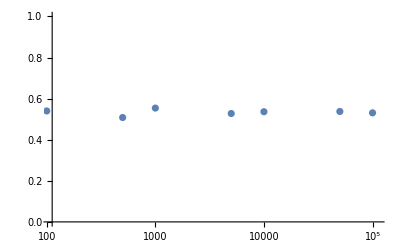

We can see that the graph is converging towards a value close to our earlier calculations which was 480/899 or about 0.53.

The graph for the estimates of getting a flush in the starting hand(excluding straight flushes since those are considered special cases).

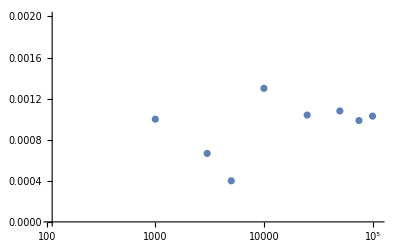

Here we can see that the graph is converging towards a value close to our earlier calculations which was 51/50344 or about 0.001.

## Code

```mathematica
simPairDeck=Join[Table[i,{i,7,14}],Table[i,{i,7,14}],Table[i,{i,7,14}],Table[i,{i,7,14}]];

simHands:=RandomSample[simPairDeck,5];
```

```mathematica
probabilitiesOFSample[x_,y_]:=Count[Sort/@Table[simHands,x],_? y]/x;
```

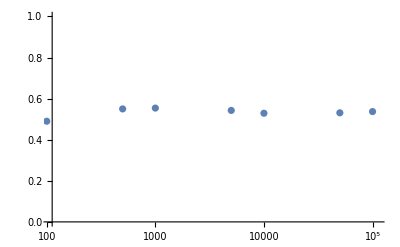

```mathematica
ListLogLinearPlot[{{10,probabilitiesOFSample[10,pairQ]},
{50,probabilitiesOFSample[50,pairQ]},
{100,probabilitiesOFSample[100,pairQ]},
{500,probabilitiesOFSample[500,pairQ]},
{1000,probabilitiesOFSample[1000,pairQ]},
{5000,probabilitiesOFSample[5000,pairQ]},
{10000,probabilitiesOFSample[10000,pairQ]},
{50000,probabilitiesOFSample[50000,pairQ]},
{100000,probabilitiesOFSample[100000,pairQ]}},
    PlotRange->{{0,111000},{0,1}}]
```

```mathematica
simFlushDeck=Join[Table[i,{i,1,4}],Table[i,{i,1,4}],Table[i,{i,1,4}],Table[i,{i,1,4}]];
```

```mathematica
simDeckOfCards=Join[Table[{1, i},{i,7,14}],Table[{2, i},{i,7,14}],Table[{3, i},{i,7,14}],Table[{4, i},{i,7,14}]];
```

```mathematica
simHands:=RandomSample[simDeckOfCards,5]
```

```mathematica
probalitiesOfFlushForN[x_]:=(numberOfFlush=0 ;For[i=1,i≤x,i++,(hand=simHands;If[( !straightQ[extractValue[hand]]&&flushQ[extractColor[hand]]),numberOfFlush+=1 ])];
numberOfFlush/x);
```

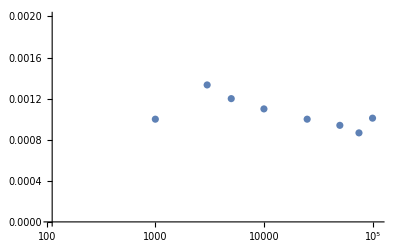

```mathematica
ListLogLinearPlot[{{3000,probalitiesOfFlushForN[3000]},
{5000,probalitiesOfFlushForN[5000]},
{1000,probalitiesOfFlushForN[1000]},
{25000,probalitiesOfFlushForN[25000]},
{75000,probalitiesOfFlushForN[75000]},
{500000,probalitiesOfFlushForN[500000]},
{10000,probalitiesOfFlushForN[10000]},
{50000,probalitiesOfFlushForN[50000]},
{100000,probalitiesOfFlushForN[100000]}},
    PlotRange->{{0,111000},{0,0.002}}]
```

Enter given data